## W^(+,-), Z^0 masses -- approximation (obsolete)

```mathematica
mWboson[k_, zL_, θH_]:=Sqrt[3/2] * k *((zL)^(-3/2)) * Sin[θH];
mZboson[mWboson_, sin2θW_]:=mWboson / Sqrt[1-sin2θW];
```

## Quark and Lepton Masses -- approximation (obsolete except neutrinos)

```mathematica
muTypeQuark[c0_, k_, zL_,θH_ ]:=If[c0< 0.5,
 (k/zL )*Sqrt[1 - 4 (c0)^2]Sin[θH/2],
 k *((zL)^-1/2 - c0)*Sqrt[4(c0)^2 - 1]Sin[θH/2]
];
mdTypeQuark[c0_, c1_, μ11_, μ1_, k_, zL_, θH_]:=If[c0<0.5,
k * ((zL)^(c0-c1-1)) * μ11/μ1*Sqrt[(1-2c0)(1+2c1)]*Sin[θH/2],
k * ((zL)^(-c1-1/2)) * μ11/μ1*Sqrt[(2c0 - 1)(2c1 + 1)]*Sin[θH/2]
];
meTypeLepton[c2_, c0_, μ11Prime_, μ2Tilde_, k_, zL_, θH_]:=If[ c2<0.5,
k * ((zL)^(-1+c2-c0)) * μ11Prime/μ2Tilde Sqrt[(2c0 + 1)(1-2c2)]Sin[θH/2],
k *  ((zL)^(-1/2 - c0)) * μ11Prime/μ2Tilde Sqrt[(2c0+1)(2c2-1)]Sin[θH/2]
];
mPsiDarkType[c0Prime_, k_, zL_, θH_]:=If[c0Prime< 0.5,
 k *(zL^(-1))Sqrt[1 - 4 (c0Prime)^2]Cos[θH/2],
 k *(zL^(-1/2 - c0Prime))Sqrt[4(c0Prime)^2 - 1]Cos[θH/2]
];
mνType [mu_, M_, mB_, c0_, zL_]:=-(2(mu)^2 *M* ((zL)^(2c0 + 1)))/((2c0 + 1) *(mB^2));
```

## Bessel basis functions FHat_αβ, F_αβ

```mathematica
Fab[α_, β_, u_, v_]:=BesselJ[α, u] BesselY[β, v] - BesselY[α, u]BesselJ[β, v];
FHat[α_, β_, u_, v_]:=BesselI[α, u] * BesselK[β, v] - Exp[-ⅈ(α - β ) * Pi] * BesselK[α,u] * BesselI[β,v];
FHatcPM[q_, c_, pm1_, pm2_, zL_]:=FHat[ c + pm1*1/2, c+pm2*1/2, q*(zL^(-1)), q  ];
```

## Fermion and Boson Basis functions S, L, SR, CR, SL, CL

```mathematica
(*   Fermions  *)
SL[λ_, z_, zL_, c_]:=-π/2 λ Sqrt[z zL]Fab[c+1/2, c+1/2, λ z, λ zL];
SR[λ_, z_, zL_, c_]:= (+π)/2 λ Sqrt[z zL]Fab[c-1/2, c-1/2, λ z, λ zL];
CR[λ_, z_, zL_, c_]:=-π/2 λ Sqrt[z zL]Fab[c-1/2, c+1/2, λ z, λ zL];
CL[λ_, z_, zL_, c_]:=(+π)/2 λ Sqrt[z zL]Fab[c+1/2, c-1/2, λ z, λ zL];



(*   Bosons   *)
Cbasis[λ_, z_, zL_]:=π/2 λ (z^(3/2)) (zL^(1/2)) Fab[3/2, 1/2, λ z, λ zL];
Sbasis[λ_, z_, zL_]:=-π/2 λ (z^(3/2)) (zL^(1/2)) Fab[3/2, 3/2, λ z ,λ zL];
Cprime[λ_, z_, zL_]:=π/2(λ^2) (z^(3/2)) (zL^(1/2)) Fab[1/2, 1/2, λ z, λ zL];
Sprime[λ_, z_, zL_]:=-π/2(λ^2) (z^(3/2)) (zL^(1/2))Fab[1/2, 3/2, λ z, λ zL];
```

## Function to integrate

```mathematica
IntIfct[Q_, f_, q_]:= q^3 Log[1+Q*f ];
IntConst[k_, zL_] := N[(k/zL)^4/(4π)^2];
```

## Q functions

```mathematica
Q0[q_, c_, zL_]:= (zL/(q^2)) * 1/(FHatcPM[q, c, 1, 1, zL]*FHatcPM[q, c, -1, -1, zL]);


Qii[q_,c0_,c1_,μ1_, μ11_, zL_]:=(zL/(q^2))*( FHatcPM[q,c0,1, 1, zL]*FHatcPM[q,c0,-1, -1, zL] + ((μ1^2) *FHatcPM[q,c0,-1, -1, zL]*FHatcPM[q,c0,-1, 1, zL]*FHatcPM[q,c1,1, 1,zL]*FHatcPM[q,c1,-1, 1, zL] )/((μ11^2) * (FHatcPM[q,c1,-1, 1, zL])^2 +( FHatcPM[q,c1,1, 1, zL])^2) )^(-1);


Qiii[q_,c0_,c2_,μ2Tilde_, μ11Prime_, zL_]:= (zL/(q^2))*(FHatcPM[q,c0,1, 1, zL] * FHatcPM[q,c0,-1, -1, zL]  + ((μ2Tilde^2)*FHatcPM[q,c0,1, 1, zL]*FHatcPM[q,c0,1, -1, zL]*FHatcPM[q,c2,-1, -1, zL]*FHatcPM[q,c2,1, -1, zL])/((μ11Prime^2) * (FHatcPM[q,c2,1, -1, zL])^2 + (FHatcPM[q,c2,-1, -1, zL])^2) )^(-1)  ;



Qiv1Aux[q_,c0_,mB_, M_ , zL_, k_]:= (zL/(q^2))*(FHatcPM[q,c0,1, 1, zL] * FHatcPM[q,c0,-1, -1, zL]  - (ⅈ* (mB^2) / (k^2))/(2(ⅈ* q* (zL)^(-1) + M/k))*FHatcPM[q,c0,-1, 1, zL]*FHatcPM[q,c0,-1, -1, zL])^(-1);
Qiv1[QAux_, θH_]:=Simplify[(QAux + Conjugate[QAux])] * (Sin[1/2 θH])^2 + Simplify[QAux * Conjugate[QAux]] * (Sin[1/2 θH])^4;



h1[q_, θH_, μ11Prime_, c2_, zL_] :=(1-μ11Prime^2)(2 * (q^2)/(zL)(1+μ11Prime^2) * FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL] + 2μ11Prime^2 + (1-μ11Prime^2)*(Sin[θH])^2 ) * (Sin[θH])^2;
h2[q_,  μ11Prime_, c2_, zL_]:=((zL^2)/(q^4))* μ11Prime^4 + 2μ11Prime^4 * (zL/(q^2))*FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL] + 
(1+μ11Prime^4)(FHatcPM[q,c2,1, 1, zL]*FHatcPM[q,c2,-1, -1, zL])^2 +
μ11Prime^2( (FHatcPM[q,c2,-1, 1, zL]*FHatcPM[q,c2,-1, -1, zL])^2 + (FHatcPM[q,c2,1, -1, zL]*FHatcPM[q,c2,1, 1, zL])^2 );
Qiv2[q_, θH_, μ11Prime_, c2_, zL_]:=((zL^2)/(q^4))* h1[q, θH, μ11Prime, c2, zL]/h2[q, μ11Prime, c2, zL];
```

## Auxiliaries

```mathematica
complexDecider[Veff_]:=If[
TrueQ[Head @ Veff==Complex],
Print["Complex Potential with magnitude:   ", Abs[Veff], "\n    Real part of     : ", Re[Veff],  "\n    Complex part of  : ", Im[Veff], "\n"]; 
,
Print["Real Potential with magnitude :  ",Veff, "\n"];
]
```

# Effective Potential Veff(θ_H)

## Fermion Contributions:

```mathematica
(***  Up-type quark contribution ***)
VeffiFCT[q_, c0_,k_, zL_, θH_, realsList_]:= Simplify[ -12 *IntConst[k, zL] *  IntIfct[Q0[q, c0, zL], (Sin[θH/2])^2, q], {realsList∈Reals}] ;

(***  Down-type quark contribution ***)
VeffiiFCT[k_, zL_, q_, c0_, c1_, μ1_, μ11_,θH_, realsList_] :=Simplify[  -12 * IntConst[k, zL] *IntIfct[Qii[q, c0, c1, μ1, μ11, zL],(Sin[θH/2])^2, q ], { realsList∈Reals}] ;

(***  Lepton contribution contribution ***)
VeffiiiFCT[k_, zL_, q_, c0_, c2_, μ2Tilde_, μ11Prime_, θH_,  realsList_] := Simplify[-4 * IntConst[k, zL] * IntIfct[ Qiii[q, c0, c2, μ2Tilde, μ11Prime, zL],(Sin[θH/2])^2, q ] ,  {realsList∈Reals} ];

(***   Neutrino Sector  ***)
Veffiv1FCT[k_, zL_, q_, c0_, mB_, M_, θH_,  realsList_] := Simplify[-4/2 * IntConst[k, zL] * IntIfct[ Qiv1[ Qiv1Aux[q, c0, mB, M, zL, k], θH ] , 1, q] ,  {realsList∈Reals} ];
Veffiv2FCT[k_, zL_, q_, θH_, μ11Prime_, c2_,  realsList_] :=Simplify[-4 * IntConst[k, zL] * IntIfct[ Qiv2[q, θH, μ11Prime, c2, zL], 1, q] ,
{realsList∈Reals} ];


(***   Dark Fermion Contribution  ***)
VeffvFCT[k_, zL_, q_, c0Prime_, θH_,  realsList_] :=Simplify[-32 * IntConst[k, zL] * IntIfct[ Q0[q, c0Prime, zL], (Cos[θH/2])^2, q] ,
{realsList∈Reals} ];
```

## Vector boson contributions

Note that in the 6D case the P_5 and P_y derivatives are different from the 5D case and results in Bessel Functions or order p = 3/2, 1/2 . Therefore the Q0 function should be indeed called with a 1 for the c argument

```mathematica
VeffWpmFCT[ξGauge_, k_, zL_, q_, θH_]:=Simplify[2(3-ξGauge^2) * IntConst[k, zL] * IntIfct[1/2*Q0[q, 1, zL], (Sin[θH])^2,q] ,
{realsList∈Reals}  ] ;
VeffZFCT[ξGauge_, k_, zL_, q_, sin2θW_, θH_]:= Simplify [(3-ξGauge^2) * IntConst[k, zL] * IntIfct[Q0[q, 1, zL]/(2(1-sin2θW)),(Sin[θH])^2,q],
{realsList∈Reals }];
VeffAzFCT[ξGauge_, k_ , zL_, q_, θH_]:=Simplify[3ξGauge^2 * IntConst[k, zL] *  IntIfct[ Q0[q, 1, zL],(Sin[θH])^2,q ],
{realsList∈Reals } ];
```

## Full Effective potential and Higgs derivatives. ∂_(H, H^2, H^3, H^4)

```mathematica
Clear[zL, k, μ11, μ1,μ11Prime, μ2Tilde, c0Prime, c0,c1, c2, θHRule, θHmin, sin2θW, ξGauge, M, mB, αEM, fH, θH];
realsList = {q, c0, c1,c2 , μ1, μ11,μ2Tilde,μ11Prime,mB, M, θH, zL, k};

VeffFermionFCT =VeffiFCT[q, c0,k, zL, θH, realsList]  +
			 VeffiiFCT[k, zL, q, c0, c1, μ1, μ11,θH, realsList]+
			 VeffiiiFCT[k, zL, q, c0, c2, μ2Tilde, μ11Prime, θH,  realsList]+
				Veffiv1FCT[k, zL, q, c0, mB, M, θH,  realsList]+
				Veffiv2FCT[k, zL, q, θH, μ11Prime, c2,  realsList] +
			VeffvFCT[k, zL, q, c0Prime, θH,  realsList];
VeffBosonFct=VeffWpmFCT[ξGauge, k, zL, q, θH] +
		       VeffZFCT[ξGauge, k, zL, q, sin2θW, θH] + 
		       VeffAzFCT[ξGauge, k , zL, q, θH];


VeffFCT = VeffFermionFCT + VeffBosonFct;
HiggsDeriv = D[VeffFCT, {θH,2}];
HiggsDeriv3 = D[VeffFCT, {θH,3}];
HiggsDeriv4 = D[VeffFCT, {θH,4}];
```

### μ11, μ11’ setting.

```mathematica
μ11Fct[μ1_,zL_,c0_,c1_]:=(4.18/172.44)*μ1*(1/(zL^(c0-c1)))*Sqrt[(1+2 c0)/(1+2 c1)];
μ11PrimeFct[μ2Tilde_,zL_,c0_,c2_]:=Which[
c0<0.5 && c2<0.5,
(1.776/172.44)*μ2Tilde*(1/(zL^(c2-c0)))*Sqrt[(1-2 c0)/(1-2 c2)],
c0<0.5&&c2>0.5,
(1.776/172.44) *μ2Tilde*(1/(zL^(0.5-c0)))*Sqrt[(1-2 c0)/(2 c2-1)],
c0>0.5&&c2<0.5,
(1.776/172.44) *μ2Tilde*(1/(zL^(c2-0.5)))*Sqrt[(2 c0-1)/(1-2 c2)],
c0>0.5&&c2>0.5,
(1.776/172.44) *μ2Tilde*Sqrt[(2 c0-1)/(2 c2-1)]
];
```

# Higgs Mass

## Higgs warping & rule

```mathematica
fHfunc[k_, zL_, sin2θW_, αEM_]:=Sqrt[ (6* sin2θW) /(4 * Pi * αEM)] * (k/Sqrt[ (1-1/zL)*(zL^3 - 1) ]);
findθHMinRule[VeffFCT_, q_, θH_] := Quiet[FindMinimum[  
Quiet[NIntegrate [VeffFCT /.{θH->θHLocal}, {q, 0, ∞}]], {θHLocal,0,1}  
][[2]]];
```

## Higgs Mass & dependent fermion masses.

```mathematica
Clear[zL, k, μ11, μ1,μ11Prime, μ2Tilde, c0Prime, c0,c1, c2, θHRule, θHmin, sin2θW, ξGauge, M, mB, αEM, fH, λListTop];


sin2θW = 0.2312;                           (* Weinberg angle *)
k= 89130;                              (* Warping constant (GeV)*)
zL =37.3;                                         (*  Warp factor  = e^(k L_5) *)

ξGauge = 0;

c0 =0.3325; (**)                                (*Up type quark bulk position*)
c1 =0.0;                                                                         (*Down type quark bulk position*)
c2 =-0.7;
c0Prime =0.5224;


μ1 = 11.18;
μ2Tilde =0.7091;

(*μ11=0.108;
μ11Prime=0.108;*)

μ11=μ11Fct[μ1,zL,c0,c1];
μ11Prime=μ11PrimeFct[μ2Tilde,zL,c0,c2];

M = -10^7;
mB = 1.145 * 10^12;
αEM=1/127.96;
fH = fHfunc[k, zL, sin2θW, αEM];

timeOut = 20;


replacementRules = {z->1, c0var->c0, zLvar->zL, μ1var -> μ1, μ11var -> μ11, c1var -> c1, μ2TildeVar -> μ2Tilde, μ11PrimeVar -> μ11Prime, c2var -> c2, c0PrimeVar -> c0Prime};
θHRule = TimeConstrained [findθHMinRule[VeffFCT, q, θH][[1]] , timeOut];


SL0 = SL[λ, z, zLvar, c0var];
SR0 = SR[λ, z, zLvar, c0var];

CR0 = CR[λ, z, zLvar, c0var];
CL0 =  CL[λ, z, zLvar, c0var];

SL1 = SL[λ, z, zLvar, c1var];
CR1 = CR[λ, z, zLvar, c1var];

SR2 = SR[λ, z, zLvar, c2var];
CL2 = CL[λ, z, zLvar, c2var];

SL0prime = SL[λ, z, zLvar, c0PrimeVar];
SR0prime = SR[λ, z, zLvar, c0PrimeVar];
(*Plot[NIntegrate[VeffFCT, {q, 0, ∞}], {θH, -0.25, 0.25}, PerformanceGoal->"Speed"]*)

If[ TrueQ[Head @ θHRule==Symbol],
Print["Timeout Reached. Aborting."];
mH = 0.0;θHmin = 0.0;mTop =  0.0;mBottom = 0.0;mTau = 0.0;
mTauNeutrino = 0.0;mPsiDark =  0.0;mW = 0.0;mZ = 0.0;
,


θHmin = θHLocal/. θHRule;

If[θHmin == 0,
Print["Trivial potential. Aborting"];
mH = 0.0;θHmin = 0.0;mTop =  0.0;mBottom = 0.0;mTau = 0.0;
mTauNeutrino = 0.0;mPsiDark =  0.0;mW = 0.0;mZ = 0.0;
,

mH = Sqrt[1/fH^2 * Quiet[NIntegrate [HiggsDeriv /.{θH ->θHLocal/. θHRule}, {q, 0, ∞}]]];

uQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2/.replacementRules;
bQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2+((μ1var^2) SR0* CR0 * SL1 *CR1)/(μ11var^2 (CR1)^2 - (SL1)^2)/.replacementRules;
tauLeptonSol = SL0 * SR0  + (Sin[θHmin/2])^2+ (μ2TildeVar^2 SL0 CL0 SR2 CL2) / (μ11PrimeVar^2 (CL2)^2  - (SR2)^2) /.replacementRules;
psiDarkQuarkSol = SL0prime * SR0prime + (Cos[θHmin/2])^2/.replacementRules;

WbosonSol = (2* Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] + λ (Sin[θHmin])^2)/.replacementRules;




guessFact = 10^(0);


uGuess=muTypeQuark[c0, k, zL,θHmin ]/k *guessFact;
WGuess = mWboson[k, zL, θHmin]/k*guessFact;
psiDarkGuess = mPsiDarkType[c0Prime, k, zL, θHmin] /k * guessFact;
tauGuess = meTypeLepton[c2, c0, μ11Prime, μ2Tilde, k, zL, θHmin] / k * guessFact;
bottomGuess = mdTypeQuark[c0, c1, μ11, μ1, k, zL, θHmin]/k*guessFact;


mTop = λ * k /.Quiet[FindRoot[uQuarkSol, {λ, uGuess}]];
mBottom =  λ * k/.Quiet[FindRoot[bQuarkSol , {λ, bottomGuess}]];
mTau =  λ * k/.Quiet[FindRoot[tauLeptonSol , {λ, tauGuess}]];
mPsiDark = λ * k /.Quiet[FindRoot[psiDarkQuarkSol, {λ, psiDarkGuess}]];



mW = λ*k/.FindRoot[WbosonSol,{λ,WGuess}];
mZ   =  mW/ Sqrt[1-sin2θW];
mZprime = λ * k /Sqrt[1-sin2θW]/. Quiet[FindRoot[WbosonSol,{λ,WGuess + π/zL} ]];


(*****  The 10^9 is here to give us the neutrino in eV *)
mTauNeutrino = mνType[mTop, M, mB, c0, zL] * 10^9;

]
]

(*Print["Effective λ Coupling of:     ",1/fH^4 NIntegrate [HiggsDeriv4 /.{θH ->θHLocal/. θHRule}, {q, 0, ∞}]];*)


Print["Higgs mass of :           ", Abs[mH], " (GeV)"];
Print["Higgs minimum <θ_H> is located at :     ", θHmin, " rads"];
Print ["Top mass of :            ",mTop, " (GeV)"];
Print ["Bottom mass of :         ",mBottom, " GeV"];
Print ["Tau lepton mass of :     ",mTau, " GeV"];
Print ["Tau Neutrino mass of :   ",     mTauNeutrino, " eV"];
Print ["Dark fermion mass of :   ", mPsiDark, " GeV"];

Print["****************"];
Print["W^(+-) mass of  :   ", mW, " GeV"];
Print["Z^0 mass of  :   ",   mZ, " GeV"];
```

Higgs mass of :           66.2459 (GeV)

Higgs minimum <θ_H> is located at :     0.0767644 rads

Top mass of :            81.8177 (GeV)

Bottom mass of :         2.06472 GeV

Tau lepton mass of :     0.656743 GeV

Tau Neutrino mass of :   0.025386 eV

Dark fermion mass of :   1900.67 GeV

****************

W^(+-) mass of  :   37.2527 GeV

Z^0 mass of  :   42.4866 GeV

```mathematica
(* Nonsense about U(1) charge fixing post symmetry breaking. *)
nq = 3;
nu=3;
nd=3;
nl = 1;
4/3*(1*nq*1/36 +1/2* nu*4/9 +1/2* nd*1/9 + 1/2 + nl*1/4)
```

```mathematica
θHmin
timeOut = 5;

replacementRules = {z->1, c0var->c0, zLvar->zL, μ1var -> μ1, μ11var -> μ11, c1var -> c1, μ2TildeVar -> μ2Tilde, μ11PrimeVar -> μ11Prime, c2var -> c2, c0PrimeVar -> c0Prime};

SL0 = SL[λ, z, zLvar, c0var];
SR0 = SR[λ, z, zLvar, c0var];

CR0 = CR[λ, z, zLvar, c0var];
CL0 =  CL[λ, z, zLvar, c0var];

SL1 = SL[λ, z, zLvar, c1var];
CR1 = CR[λ, z, zLvar, c1var];

SR2 = SR[λ, z, zLvar, c2var];
CL2 = CL[λ, z, zLvar, c2var];

SL0prime = SL[λ, z, zLvar, c0PrimeVar];
SR0prime = SR[λ, z, zLvar, c0PrimeVar];

uQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2/.replacementRules;
bQuarkSol = SL0 * SR0  + (Sin[θHmin/2])^2+((μ1var^2) SR0* CR0 * SL1 *CR1)/(μ11var^2 (CR1)^2 - (SL1)^2)/.replacementRules;
tauLeptonSol = SL0 * SR0  + (Sin[θHmin/2])^2+ (μ2TildeVar^2 SL0 CL0 SR2 CL2) / (μ11PrimeVar^2 (CL2)^2  - (SR2)^2) /.replacementRules;
psiDarkQuarkSol = SL0prime * SR0prime + (Cos[θHmin/2])^2/.replacementRules;

WbosonSol = (2* Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] + λ (Sin[θHmin])^2)/.replacementRules;

n=3;
guessFact = 10^(-0);


uGuess=muTypeQuark[c0, k, zL,θHmin ]/k *guessFact;
WGuess = mWboson[k, zL, θHmin]/k*guessFact;
psiDarkGuess = mPsiDarkType[c0Prime, k, zL, θHmin] /k * guessFact;
tauGuess = meTypeLepton[c2, c0, μ11Prime, μ2Tilde, k, zL, θHmin] / k * guessFact;
bottomGuess = mdTypeQuark[c0, c1, μ11, μ1, k, zL, θHmin]/k*guessFact;


(*λListTop = Quiet[Reduce[uQuarkSol==0 && uGuess< λ <  n π /zL, λ]];
λListPsiDark = Quiet[Reduce[psiDarkQuarkSol==0 && psiDarkGuess< λ < n π /zL, λ]];*)
(*λListWpm= Quiet[Reduce[WbosonSol==0 && WGuess< λ < n π /zL, λ]];*)

mTop = λ * k /.Quiet[FindRoot[uQuarkSol, {λ, uGuess}]];
mBottom =  λ * k/.Quiet[FindRoot[bQuarkSol , {λ, bottomGuess}]];
mTau =  λ * k/.Quiet[FindRoot[tauLeptonSol , {λ, tauGuess}]];
mPsiDark = λ * k /.Quiet[FindRoot[psiDarkQuarkSol, {λ, psiDarkGuess}]];



mW = λ*k/.Quiet[FindRoot[WbosonSol,{λ,WGuess}]];
mZ   =  mW/ Sqrt[1-sin2θW];
mZprime = λ * k /Sqrt[1-sin2θW]/. Quiet[FindRoot[WbosonSol,{λ,WGuess + π/zL} ]];


(*mTop =  Extract[Extract[λListTop , {1}],{2}]*k;*)
(*mPsiDark =  Extract[Extract[λListPsiDark , {1}],{2}]*k;*)
(*mW      =  Extract[Extract[λListWpm , {1}],{2}]*k;*)
(*mZprime = Extract[Extract[λListWpm , {2}],{2}]*k /Sqrt[1-sin2θW];*)


Print["The 1st KK mode for the top quark: ", mTop];
Print["The 1st KK mode for the bottom quark: ", mBottom];
Print["The 1st KK mode for the tau lepton: ", mTau];
Print["The 1st KK mode for the dark fermion multiplet: ", mPsiDark];
Print["The 1st KK mode for the W^(+-) bosons: ", mW];
Print["The 1st KK mode for the Z^0 bosons: ", mZ];
Print["The 2nd KK mode for the Z^0 bosons: ", mZprime];
```

0.149481

The 1st KK mode for the top quark: 170.564

The 1st KK mode for the bottom quark: 4.21496

The 1st KK mode for the tau lepton: 1.4037

The 1st KK mode for the dark fermion multiplet: 2043.76

The 1st KK mode for the W^(+-) bosons: 79.6688

The 1st KK mode for the Z^0 bosons: 90.8618

The 2nd KK mode for the Z^0 bosons: 9389.5

### Approximation Comparisons

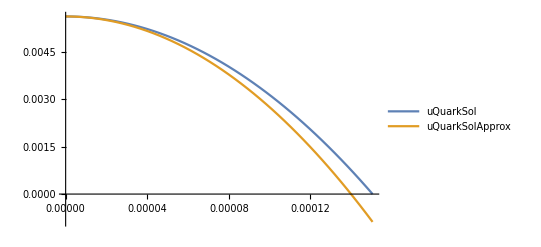

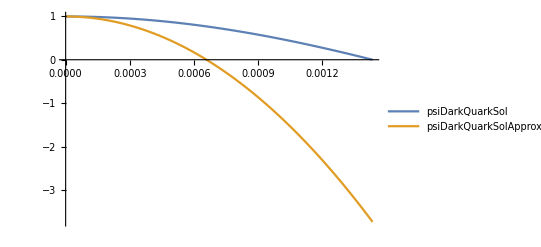

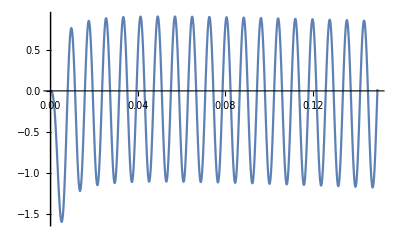

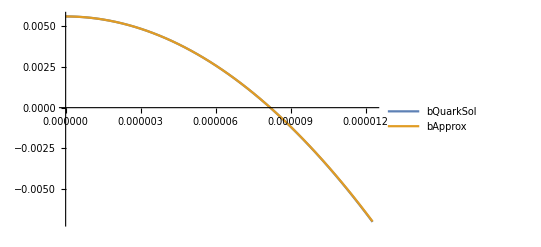

```mathematica
zL = 21;
SRapproxLess=λ zLvar^(1-c0var) / (2 * (1/2 - c0var));
SLapproxLess = - λ zLvar^(c0var + 1) / (2 * (1/2 + c0var));

SRapproxGreaterPrime=λ zLvar^(c0PrimeVar) / (2 * ( c0PrimeVar - 1/2));
SLapproxGreaterPrime = - λ zLvar^(c0PrimeVar + 1) / (2 * (1/2 + c0PrimeVar));

(*Sapprox =-1/2 λ zLvar;
Cprimeapprox = λ^2 zLvar Log[zLvar];*)

uQuarkSolApprox = SLapproxLess SRapproxLess+ (Sin[θHmin/2])^2/.replacementRules;
psiDarkQuarkSolApprox = SLapproxGreaterPrime SRapproxGreaterPrime+ (Cos[θHmin/2])^2/.replacementRules;
wApprox = Normal[Series[WbosonSol, {λ, 0, 3}]];
bApprox = Normal[Simplify[Series[bQuarkSol, {λ, 0, 2}]]];




Plot[{uQuarkSol, uQuarkSolApprox }, {λ, 0, mTop/k} , PlotLegends->"Expressions"]
Plot[{psiDarkQuarkSol, psiDarkQuarkSolApprox}, {λ, 0, mPsiDark/k} , PlotLegends->"Expressions"]

Plot[{WbosonSol}, {λ, WGuess, WGuess + π/zL}, PlotLegends->"Expressions", Epilog->{InfiniteLine[{WGuess,0},{0,1}]}]

Plot[{bQuarkSol, bApprox }, {λ, 0, 1.5mBottom/k} , PlotLegends->"Expressions"]
```

```mathematica
zL = 68;
WbosonSol = (2* Cprime[λ, z, zLvar]*Sbasis[λ, z, zLvar] + λ (Sin[θHmin])^2)/.{z->1, zLvar->zL};

WGuess = mWboson[k, zL, θHmin]/k;
WGuess* k
(*λListWpm=Reduce[WbosonSol==0 && (WGuess)*10^(-1)< λ < WGuess*1.5, λ];*)

λ*k/.FindRoot[WbosonSol,{λ,WGuess}]
λ * k /Sqrt[1-sin2θW]/. FindRoot[WbosonSol,{λ,WGuess + π/zL} ]
```

33.9922

34.248

4765.32

171.157

2043.71